# EDMD Built

## Initialization

### Numerical Variable Definition

```mathematica
eventspercycle = 10; (*Events per sphere per cycle*)
n=300; (*Number of Spheres*)
steps=eventspercycle n; (*steps per cycle*)
ipf=.3; (*Initial packing fraction*)
rate=.03; (*Growth rate (relative)*)
mpressure=100; (*max pressure*)
gtime = 0 ;(*global time*)
bratio = .4;
rratio = .4;
size = 1;
steps=eventspercycle n; (*steps per cycle*)
```

### Global Variables

Initializes radii, positions, velocities, nextevents, heap, hash, cellMatrix, cellA, lastupdates in that order.

```mathematica
gtime=0;
radii=rlist[ipf, size, n, bratio, rratio];
nrows=optimalGrid[size, radii⟦1⟧];
positions=createDisks[radii, size];
velocities = velocityInit[size, n];
setInitialEvents[n]
changeBins[nrows]
lastupdates=Table[0, n];
nestpositions={positions};
nestradii={radii};
pf={packingFraction};
```

### Process Variables

```mathematica
nchecks=0;
ntrans=0;
ncollisions = 0;
counter = 0;
nevents=0;
```

## Process

### Step

Processes a single event.

```mathematica
nextevents
```

{{0,1,∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
processEvent
```

check event error

```mathematica
nextevents
```

{{0.,1,-∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
obtainMin@heap
```

{0,2}

```mathematica
(processEvent//AbsoluteTiming)⟦1⟧
```

0.00238216

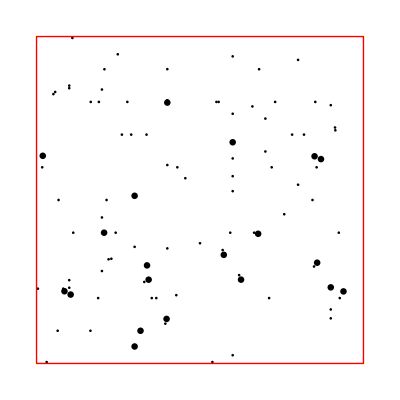

```mathematica
displayParticles[positions, radii, size]
```

### Cycle

```mathematica
positions=positions+velocities(gtime-lastupdates);
```

```mathematica
radii=radii(1+gtime rate);
```

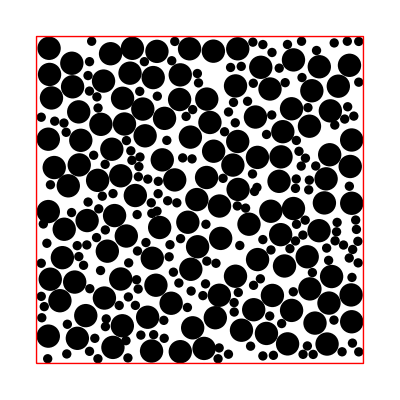

```mathematica
displayParticles[positions, radii, size]
```

```mathematica
overlapQ
```

False

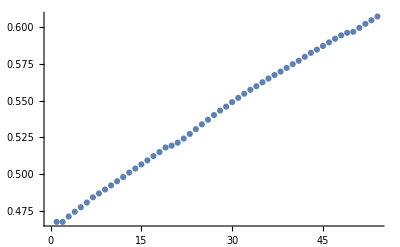

```mathematica
pf//ListPlot
```

```mathematica
nevents=0;
(Process[];)//AbsoluteTiming
```

1 already overlapping, C, d:-0.0000249018 1.95515×10^-7

spheres are already overlapping -0.0000249018

$Aborted

```mathematica
nextevents
```

```mathematica
synchronize[]
```

```mathematica
pf
```

{0.467469,0.467469,0.47115,0.474364,0.477462,0.480662,0.484224,0.486863,0.489523,0.492335,0.495185,0.498058,0.501062,0.503787,0.506624,0.509359,0.512285,0.514992,0.518129,0.51941,0.521419,0.524233,0.527372,0.530642,0.533923,0.537052,0.540243,0.543302,0.546003,0.549063,0.551956,0.554777,0.557415,0.559866,0.562564,0.565149,0.567512,0.569845,0.572347,0.574891,0.577217,0.579917,0.582627,0.584789,0.587289,0.589736,0.592236,0.594539,0.596261,0.596953,0.59962,0.602355,0.604794,0.607394}

```mathematica
positionsz=positions+velocities(gtime - lastupdates);
positionsz[[51]]
```

{0.960457,0.912087}

```mathematica
lastupdates[[49]]
```

```mathematica
positions[]
```

0.17811

```mathematica
For[i=1, i<n, i++,
For[j=i+1, j≤n, j++,
If[!overlapC[{positionsz⟦i⟧, radii⟦i⟧}, {positionsz⟦j⟧, radii⟦j⟧}],
Print[i," ", j]
]
]
]
```

```mathematica
overlapQ
```

True

```mathematica
ListPlot@pf
```

-Graphics-

```mathematica
pf//Length
```

19

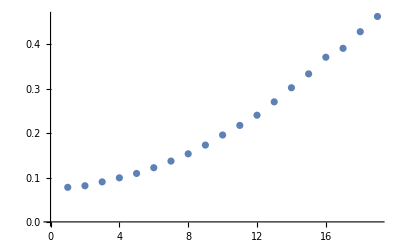

```mathematica
ListPlot@pf
```

9

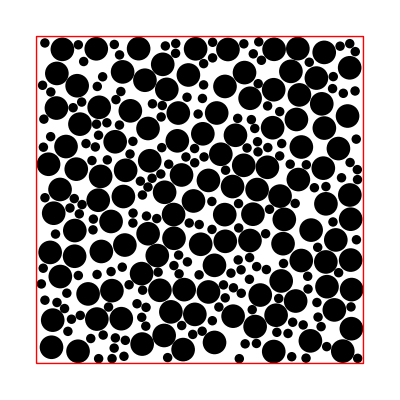

```mathematica
nrows
```

```mathematica
overlapQ
```

False

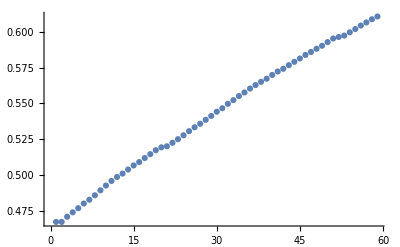

```mathematica
pf//ListPlot
```

```mathematica
Manipulate[displayParticles[nestpositions⟦i⟧, nestradii⟦i⟧, size], {i, 1, nestpositions//Length, 1}]
```